```mathematica
(* Create global definitions and set up workspace for all subsequent work *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
<<setup_workspace.m;
<<setup_definitions.m;
```

Exporting:discreteApprox

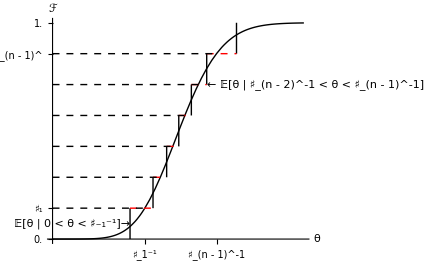

```mathematica
(* Read in baseline parameters and construct baseline shocks then make discreteApprox figure *)
<<setup_params.m;
<<setup_shocks.m;
<<discreteApprox!Plot.m;
```

```mathematica
(* Set up for solution of 2 period model and construction of figures *)
<<setup_params_2period.m;
<<setup_grids.m;
<<setup_shocks.m;
<<setup_lastperiod.m;
<<setup_PerfectForesightSolution.m;
```

Use the 'method of moderation,' with only upper bound.

Exporting:IntExpFOCInvPesReaOptNeedHiPlot

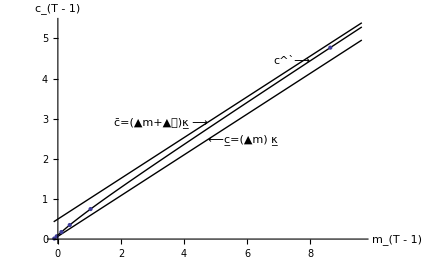

Exporting:IntExpFOCInvPesReaOptNeedHiValuePlot

```mathematica
<<2PeriodIntExpFOCInvPesReaOptHi!Plot.m;
```

Use the 'method of moderation, with both upper and lower bounds.'

Exporting:IntExpFOCInvPesReaOptNeedBothPlot

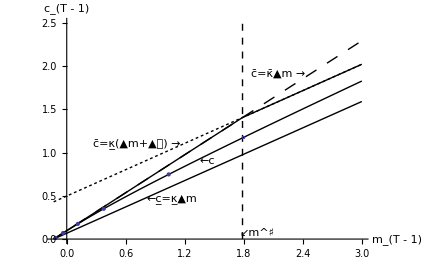

Exporting:IntExpFOCInvPesReaOptNeedBothValuePlot

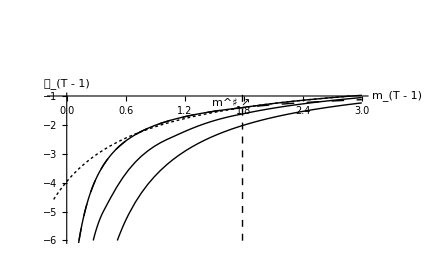

Difference in consumption function before and after refinement.

Exporting:IntExpFOCInvPesReaOptBothGapPlot

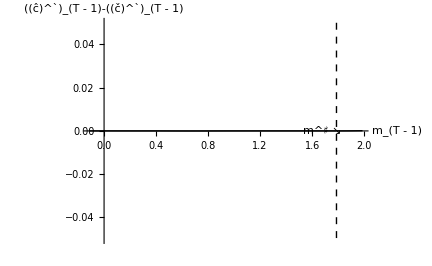

Exporting:IntExpFOCInvPesReaOptBothValueGapPlot

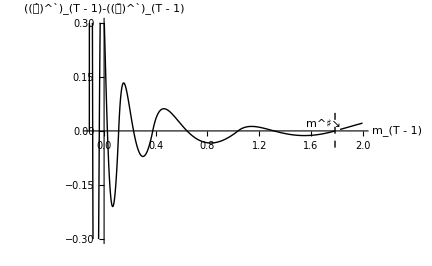

```mathematica
<<2PeriodIntExpFOCInvPesReaOptBoth!Plot.m;
```